# MeSH subject weighted pivot-size

主要論文個別にpivot - size：すなわち、自身のMeSHベクトルと（被）引用MeSHベクトルの CosineDistance をとる。（被）引用MeSHベクトルは複数である可能性があるが、引用する/される論文を集合とした「重みつき合成」ベクトル。各世代の共時的分析。当該世代のtop論文が当該世代までの累積引用に対してどの程度のpivotが生じているのか、を見る。

通時的分析のためのセレクションをここで行う：
各グループで1985の代表より以下を条件に選択する：1)BaseとCitedそれぞれにMeSHが付与されていること、2)pubyearが古いこと、3)可能ならば全てのグループでpubyearを合わせる。

pivot-sizeを追うには、ある程度論文を選択する必要があると思われる：

publish year：できるだけ出版が古いもの

MeSH付与：引用が低い論文でもそれなりに引用があるものである必要がある -> 76%クラスは難しいかも

## pivot計算

## PMID to MeSH rule

Assc : PMIDtoMeSHDruleASC

```mathematica
AbsoluteTiming[Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];]
```

{149.73,Null}

## 主要論文とそれを引用する論文

### 元Data

変数: topCitingCitedArt1Perc[YYYY, "citing rule"]

```mathematica
mainCitingartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainCitingartfiles];
```

#### 重みに関する定義

```mathematica
toWeighted[{}]:={}
toWeighted[l_]:=l/Length[l]
```

```mathematica
weightCount[t_Times]:=Rule[t[[2]],t[[1]]]
weightCount[t_String]:=Rule[t,1]
```

#### MeSHベクトルのコサイン距離定義

重みなし：

```mathematica
meshCosD[l1_,l2_]:=Module[{terms,cv1,cv2},
terms=Union[Flatten[{l1,l2}]];
cv1=Map[Count[l1,#]&,terms];
cv2=Map[Count[l2,#]&,terms];
CosineDistance[cv1,cv2]
]
```

重みつきターム用：

```mathematica
meshCosDWN[l1_/;Head[l1]=!=List,l2_]:=Indeterminate
meshCosDWN[l1_,l2_/;Head[l2]=!=List]:=Indeterminate
meshCosDWN[{},{}]:=Indeterminate
meshCosDWN[l1_List,l2_List]:=Module[{terms,cl1,cl2,tv1,tv2},
cl1=Association[Map[weightCount,l1]];
cl2=Association[Map[weightCount,l2]];
terms=Union[Flatten[{Keys[cl1],Keys[cl2]}]];
tv1=Map[cl1[#]&,terms]/._Missing->0;
tv2=Map[cl2[#]&,terms]/._Missing->0;
CosineDistance[tv1,tv2]
]
```

### 主要論文のMeSHベクトル

```mathematica
Do[mainArtBaseTermWN[n]=Map[toWeighted[Cases[#,_String]]&,Map[Flatten,Map[PMIDtoMeSHDruleASC,Map[Union,Map[#[[2]]&,topCitingCitedArt1Perc[n, "citing rule"],{2}]],{2}]]],{n,1950,2020,5}]
```

```mathematica
Table[mainArtBaseTermWN[n]//Length,{n,1950,2020,5}]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

```mathematica
Position[mainArtBaseTermWN[1955],x_/;x=!={},1]
```

{{0},{4},{6},{12},{14},{16},{18},{19},{23},{24},{25},{26},{27},{28},{29}}

```mathematica
mainArtBaseTermWN[1955][[12]]
```

{Humans/2,Salts/2}

### 主要論文を引用する(“citing”)論文集合のMeSHベクトル

```mathematica
Do[mainArtCitingTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC[#[[1]]]&,topCitingCitedArt1Perc[n, "citing rule"],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

```mathematica
Table[mainArtCitingTermWN[n]//Length,{n,1950,2020,5}]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

### 主要論文全てのciting-pivotの計算

1950 年代は外す。

```mathematica
mainArtBaseTermWN[1950]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
(citingPivotTbl=Table[Inner[meshCosDWN,mainArtBaseTermWN[n],mainArtCitingTermWN[n],List]//N,{n,1955,2020,5}])//TableForm
```

0. | 0. | 0. | 0.671183 | 0. | 0.692862 | 0. | 0. | 0. | 0. | 0. | 0.612694 | 0. | 0.414076 | 0. | 0.289127 | 0. | 0.607932 | 0.479033 | 0. | 0. | 0. | 0.516023 | 0.853577 | 0.29458 | 0.879626 | 0.582591 | 0.189687 | 0.35143 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.888156 | 0.255975 | 0. | 0. | 0. | 0.77442 | 0. | 0. | 0. | 0.186512 | 0.665872 | 0.500224 | 0. | 0.751576 | 0.600649 | 0.464774 | 0.350721 | 0. | 0.223583 | 0.511959 | 0.244166 | 0. | 0.472351 | 0.398487 | 0.294918 | 0. | 0.278848 | 0.428277 | 0.390601 | 0.222353 | 0. | 0.654495 | 0.443222 | 0.555264 | 0. | 0.57852 | 0.72182 | 0. | 0.35782 | 0. | 0.613285 | 0.673041 | 0.16122 | 0.597103 | 0.758765 | 0.70508 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.878496 | 0.293959 | 0.726435 | 0. | 0.772379 | 0. | 0. | 0. | 0.685082 | 0. | 0.526463 | 0.310143 | 0.784966 | 0.607048 | 0. | 0.45154 | 0.450166 | 0.329484 | 0.837089 | 0.36814 | 0.746684 | 0.505131 | 0.667563 | 0.544474 | 0.308716 | 0.41827 | 0.721608 | 0.190923 | 0.737777 | 0.680888 | 0.467842 | 0.513487 | 0.436565 | 0. | 0.588781 | 0.596187 | 0.913884 | 0.827462 | 0.534556 | 0. | 0.819712 | 0.47445 | 0.5828 | 0.276564 | 0.521411 | 0. | 0.772761 | 0. | 0. | 0.502339 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.924878 | 0.665397 | 0.685685 | 0.372471 | 0.715745 | 0.756602 | 0.604507 | 0.616637 | 0.586097 | 0.857693 | 0.539056 | 0.610721 | 0.537893 | 0.38899 | 0. | 0.435965 | 0.407265 | 0.692075 | 0.716066 | 0.401123 | 0.742009 | 0. | 0.853616 | 0.634707 | 0.334197 | 0.947735 | 0. | 0.650289 | 0.723607 | 0. | 0.478747 | 0.913823 | 0.358688 | 0.59345 | 0.63321 | 0. | 0.48955 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.942021 | 0.712085 | 0.678745 | 0.728289 | 0.780614 | 0.620949 | 0.713978 | 0.40922 | 0.574615 | 0.658419 | 0.728412 | 0.494457 | 0.735577 | 0.696575 | 0.500513 | 0.598608 | 0.432236 | 0.876203 | 0.954911 | 0.745818 | 0.9209 | 0.598536 | 0.561636 | 0.653727 | 0. | 0.439525 | 0.910705 | 0.674013 | 0.802387 | 0.709969 | 0.618673 | 0.441228 | 0.728441 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.959294 | 0.741414 | 0.698169 | 0.776705 | 0.7348 | 0.757591 | 0.810446 | 0.764713 | 0.52361 | 0.632464 | 0.596064 | 0.68055 | 0.423373 | 0.765089 | 0.948105 | 0.487138 | 0.536513 | 0.688 | 0.763354 | 0. | 0.960641 | 0.764846 | 0.641534 | 0.803676 | 0.652696 | 0.697223 | 0.574241 | 0.444028 | 0.917559 | 0.842411 | 0.856483 | 0.445731 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.966356 | 0.840877 | 0.570673 | 0.745695 | 0.75662 | 0.700785 | 0.630057 | 0.779776 | 0.942461 | 0.812514 | 0.823596 | 0.787927 | 0.903754 | 0.535649 | 0.64295 | 0.580884 | 0.616457 | 0.674794 | 0.457805 | 0. | 0.516885 | 0.961667 | 0.832156 | 0.758924 | 0.664209 | 0.664094 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.97043 | 0.867651 | 0.585527 | 0.718677 | 0.944508 | 0.649087 | 0.678882 | 0.82129 | 0.74562 | 0.801157 | 0.505969 | 0.765778 | 0.651884 | 0.700872 | 0.600905 | 0.550744 | 0.682718 | 0.831166 | 0.798898 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.972816 | 0.891825 | 0.75047 | 0.944293 | 0.59074 | 0.698718 | 0.652177 | 0.578792 | 0.661111 | 0.819657 | 0.746905 | 0.539619 | 0.573652 | 0.712933 | 0.810964 | 0.750735 | 0.768715 | 0.616664 | 0.792157 | 0.692491 | 0.577029 | 0.701286 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.97374 | 0.90188 | 0.760024 | 0.939382 | 0.593827 | 0.704498 | 0.689035 | 0.587482 | 0.652278 | 0.658342 | 0.584229 | 0.770521 | 0.550002 | 0.819339 | 0.747872 | 0.814028 | 0.586559 | 0.79303 | 0.654142 | 0.618172 | 0.76995 | 0.724746 | 0.601275 | 0.694788 | 0.879271 | 0.799109 | 0.701351 | 0.83647 | 0.804224 | 0.901342 | 0.666333 | 0.657162 | 0.747237 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.973974 | 0.906651 | 0.762782 | 0.933887 | 0.594728 | 0.707274 | 0.683617 | 0.589774 | 0.652543 | 0.658842 | 0.587683 | 0.657311 | 0.774713 | 0.552871 | 0.407742 | 0.748919 | 0.81936 | 0.813484 | 0.593416 | 0.585312 | 0.716038 | 0.790847 | 0.619717 | 0.87804 | 0.770596 | 0.602997 | 0.796872 | 0.661458 | 0.695158 | 0.686359 | 0.701787 | 0.746054 | 0.804342 | 0.837283 | 0.601549 | 0.792717 | 0.704779 | 0.901524 | 0.453896 | 0.657421 | 0.439073 | 0.622188 | 0.772869 | 0.579224 | 0.624069 | 0.870345 | 0.558793 | 0. | 0.546344 | 0.604943 | 0.973247 | 0.799483 | 0.750549 | 0.719549 | 0.70441 | 0.84792 | 0.650555 | 0.818255 | 0.712444 | 0.754989 | 0.941979 | 0.538839 | 0.747008 | 0.442637 | 0.789661 | 0.581994 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.974211 | 0.910759 | 0.929472 | 0.763535 | 0.707407 | 0. | 0.595114 | 0.396571 | 0.677266 | 0.663489 | 0.590356 | 0.5908 | 0.652403 | 0.586375 | 0.656779 | 0.822012 | 0.776009 | 0.553787 | 0.597814 | 0.75231 | 0.660468 | 0.587404 | 0.678071 | 0.819383 | 0.465924 | 0.637445 | 0.696192 | 0.774558 | 0.877417 | 0. | 0.789535 | 0.628505 | 0.689943 | 0.652929 | 0.772534 | 0.785815 | 0.70205 | 0.793552 | 0.568114 | 0.603214 | 0.797255 | 0.652934 | 0.695372 | 0.745654 | 0.584793 | 0.669194 | 0.433303 | 0.702978 | 0.805628 | 0. | 0.635111 | 0.838241 | 0.664983 | 0.627001 | 0.453969 | 0.657374 | 0.901645 | 0.647585 | 0.598326 | 0.399299 | 0.784939 | 0.508683 | 0.577519 | 0. | 0.94114 | 0.379188 | 0.772726 | 0.625161 | 0.628384 | 0.580028 | 0.870933 | 0.559577 | 0.611843 | 0.607339 | 0.642123 | 0.546125 | 0.974441 | 0.658382 | 0.531608 | 0.713331 | 0.893242 | 0.751356 | 0.740218 | 0.47342 | 0.71951 | 0.389267 | 0. | 0.792134 | 0.847786 | 0.693571 | 0.712593 | 0.762735 | 0.474064 | 0.70359 | 0.818318 | 0.44585 | 0.837942 | 0.563555 | 0.585677 | 0.686574 | 0.56736 | 0.729314 | 0.604876 | 0.696792 | 0.591782 | 0.704507 | 0.60659 | 0.540032 | 0.746766 | 0.607484 | 0.684364 | 0.741757 | 0.408539 | 0.872526 | 0.387746 | 0.439853 | 0.48959 | 0.576726 | 0.970997 | 0.627349 | 0.635507 | 0.600686 | 0.679894 | 0.702513 | 0.533249 | 0.85656 | 0.756956 | 0.611718 | 0.544003 | 0.793482 | 0.484564 | 0.623505 | 0.484063 | 0.630383 | 0.546764 | 0.479877 | 0.741869 | 0.509323 | 0.610359 | 0.80839 | 0.587044 | 0.356911 | 0.683164 | 0.502632 | 0.601391 | 0.468111 | 0.644946 | 0.734577 | 0.499813 | 0.502403 | 0.657809 | 0.892093 | 0.486091 | 0.29813 | 0.894623 | 0.664 | 0.684782 | 0.596995 | 0.784821 | 0.773974 | 0.456063 | 0.361536 | 0.665985 | 0.516595 | 0.661017 | 0.644584 | 0.738949 | 0.693427 | 0.434195 | 0.588108 | 0.690581 | 0.508314 | 0.405379 | 0.753638 | 0.246968 | 0.612034 | 0.666012 | 0.546342 | 0.58722 | 0.555884 | 0.712855 | 0.4275 | 0.438624 | 0.503945 | 0.385208 | 0.448831 | 0.761978 | 0.645819 | 0.547664 | 0.705856 | 0.455928 | 0.516824 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.914038 | 0.973055 | 0.930373 | 0. | 0.764744 | 0.735682 | 0.398466 | 0.691337 | 0.608761 | 0.70689 | 0.672625 | 0.595303 | 0.470697 | 0.66725 | 0.573821 | 0.577863 | 0.702734 | 0.640163 | 0.834568 | 0.582475 | 0.665636 | 0.606226 | 0.590998 | 0.524778 | 0.36355 | 0. | 0.651869 | 0.875067 | 0.585207 | 0.400207 | 0.770486 | 0.613338 | 0.683145 | 0.703932 | 0.671671 | 0.918683 | 0.544823 | 0.601468 | 0.655859 | 0.486044 | 0.757718 | 0.60512 | 0.554636 | 0. | 0.646969 | 0.776163 | 0.682767 | 0.38259 | 0.615736 | 0.870287 | 0.51798 | 0.960189 | 0.663143 | 0.680169 | 0.591719 | 0.711061 | 0.496127 | 0.499903 | 0.819172 | 0.625789 | 0.504261 | 0.524845 | 0.572846 | 0.652033 | 0.694992 | 0.61454 | 0.749284 | 0.390036 | 0.858072 | 0.483931 | 0.648513 | 0.64708 | 0. | 0.603216 | 0.628773 | 0.604517 | 0.808298 | 0.784345 | 0.637637 | 0. | 0.563603 | 0.544531 | 0.799627 | 0.212483 | 0.645336 | 0.691766 | 0.698371 | 0.766583 | 0.76926 | 0. | 0.656991 | 0.512598 | 0.781776 | 0.534035 | 0.378044 | 0.72773 | 0.489416 | 0.528962 | 0.547691 | 0.792325 | 0.584782 | 0.598708 | 0.580906 | 0.62854 | 0.46278 | 0.41204 | 0.468232 | 0.570586 | 0.773193 | 0.476359 | 0.789971 | 0.390638 | 0.54792 | 0.631941 | 0.747758 | 0.63077 | 0.60368 | 0.744946 | 0.523064 | 0.742582 | 0.943434 | 0.655248 | 0.429802 | 0.379757 | 0.561141 | 0.656121 | 0.752503 | 0.695371 | 0.349356 | 0.655293 | 0.555204 | 0.409876 | 0.883607 | 0.604331 | 0.61262 | 0.806018 | 0.335398 | 0.704305 | 0.813334 | 0.570949 | 0.763771 | 0.977695 | 0.561341 | 0.737242 | 0.661746 | 0. | 0.496727 | 0.631107 | 0.837494 | 0.57267 | 0.494589 | 0.444408 | 0.656346 | 0.577839 | 0.45483 | 0.543784 | 0.432209 | 0.587648 | 0.511596 | 0.488289 | 0.807915 | 0.54508 | 0.90184 | 0.775246 | 0.609968 | 0.457891 | 0.667444 | 0.511894 | 0.452388 | 0.345974 | 0.662287 | 0. | 0.890526 | 0.427906 | 0.701133 | 0.451164 | 0.524497 | 0.747987 | 0.763634 | 0.522524 | 0.250895 | 0.465788 | 0.689945 | 0.582032 | 0.488024 | 0.575916 | 0.609647 | 0.453668 | 0.390839 | 0.706513 | 0.170818 | 0.62149 | 0.951517 | 0.766809 | 0.506479 | 0.494835 | 0.471206 | 0.38511 | 0.527695 | 0.321637 | 0.535867 | 0.544489 | 0.534755 | 0.772807 | 0.97557 | 0.616258 | 0.588053 | 0.72171 | 0.819617 | 0.649525 | 0.625225 | 0.276824 | 0.529499 | 0.576203 | 0.411676 | 0.561125 | 0.61047 | 0.750732 | 0.871141 | 0.627795 | 0.37291 | 0.86147 | 0.258316 | 0.381608 | 0.491157 | 0.540758 | 0.380826 | 0.287809 | 0.69403 | 0.83845 | 0.601521 | 0.545429 | 0. | 0.49715 | 0.738129 | 0.822257 | 0.315262 | 0.186688 | 0.724644 | 0.491908 | 0.483636 | 0.772479 | 0.505036 | 0.633831 | 0. | 0.33563 | 0.760553 | 0.432226 | 0.616081 | 0.802047 | 0.721976 | 0.54994 | 0.791307 | 0.572489 | 0.57484 | 0.713602 | 0.505562 | 0.671797 | 0.515787 | 0.677297 | 0.531676 | 0.497822 | 0.522612 | 0.611271 | 0.401811 | 0.424484 | 0.847706 | 0.708512 | 0.374826 | 0.724087 | 0.445375 | 0.451804 | 0.54791 | 0.312273 | 0.509143 | 0.808078 | 0.580694 | 0.594947 | 0.489849 | 0.495089 | 0.474106 | 0.590145 | 0.501279 | 0.669497 | 0.552686 | 0.544145 | 0.427844 | 0.369932 | 0.991165 | 0.710547 | 0.690279 | 0.532617 | 0.40929 | 0.468233 | 0.386634 | 0.542276 | 0.458781 | 0.778805 | 0.714268 | 0.633915 | 0.702667 | 0.616453 | 0.618953 | 0.583534 | 0.6304 | 0.597944 | 0.579346 | 0.641593 | 0.703037 | 0.818463 | 0.745053 | 0.472159 | 0.505327 | 0.706121 | 0.707736 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.915922 | 0.971639 | 0.771993 | 0.933682 | 0. | 0.720168 | 0.401818 | 0.765735 | 0.414948 | 0.478075 | 0.632275 | 0.695784 | 0.921691 | 0.585192 | 0.729916 | 0.706981 | 0.96516 | 0.551893 | 0.579516 | 0.633038 | 0.517162 | 0.667773 | 0.791286 | 0.701815 | 0.562258 | 0.661098 | 0.557814 | 0.861007 | 0.595457 | 0.673435 | 0.851078 | 0.693389 | 0.702918 | 0.557218 | 0.59731 | 0.966881 | 0.611772 | 0.668176 | 0.662081 | 0.703222 | 0.597736 | 0.643371 | 0.844423 | 0.837298 | 0.829465 | 0.811286 | 0.517943 | 0.571465 | 0.727243 | 0.686155 | 0.475335 | 0.770881 | 0.662322 | 0.585605 | 0.488369 | 0. | 0.86768 | 0.692634 | 0.665086 | 0.728876 | 0.528966 | 0.606704 | 0.517608 | 0.390441 | 0.524369 | 0.222516 | 0.700093 | 0.532338 | 0.636724 | 0.386341 | 0.622725 | 0. | 0.756636 | 0.594582 | 0.414117 | 0.727954 | 0.602744 | 0.744358 | 0.505889 | 0.590891 | 0. | 0.693997 | 0.576272 | 0.665634 | 0.259579 | 0.598568 | 0.527904 | 0.63757 | 0.38971 | 0.768384 | 0.652835 | 0.58325 | 0.507908 | 0.651837 | 0.623267 | 0.562788 | 0.573929 | 0.465612 | 0. | 0.768064 | 0.392742 | 0.994137 | 0.821143 | 0.691717 | 0.78096 | 0.672113 | 0.862 | 0.499732 | 0.599241 | 0.518623 | 0.655972 | 0.666621 | 0.321785 | 0.603941 | 0.693258 | 0.807313 | 0.438853 | 0.764924 | 0.913372 | 0. | 0.586536 | 0.869933 | 0.587693 | 0.746535 | 0.796316 | 0.550433 | 0.580494 | 0.862061 | 0.48412 | 0.477769 | 0.65576 | 0.579452 | 0.632013 | 0.747641 | 0. | 0.69153 | 0.57597 | 0.327068 | 0.460768 | 0.267711 | 0.408872 | 0.809616 | 0.603708 | 0.616237 | 0.554085 | 0.417644 | 0.788867 | 0.775114 | 0.584082 | 0.543837 | 0.667345 | 0.776185 | 0.646688 | 0.602999 | 0.487269 | 0.533754 | 0.52654 | 0.648261 | 0.667433 | 0.437304 | 0.600786 | 0.79283 | 0.69695 | 0.556293 | 0.722411 | 0.681939 | 0.991591 | 0.30571 | 0.655797 | 0.642425 | 0.709659 | 0.390912 | 0.798306 | 0.59075 | 0.497308 | 0.368382 | 0.388888 | 0.433028 | 0.497541 | 0.533617 | 0.794105 | 0.974555 | 0.819048 | 0.459187 | 0.662919 | 0.558671 | 0.615513 | 0.333648 | 0.468443 | 0.650362 | 0.764202 | 0.449461 | 0.581766 | 0.421531 | 0.721299 | 0.710005 | 0.558513 | 0.645006 | 0.52086 | 0.654417 | 0.580334 | 0.385367 | 0.511028 | 0. | 0.567135 | 0.56447 | 0.796206 | 0.884358 | 0.696948 | 0.569815 | 0.496647 | 0.350331 | 0.426977 | 0.748296 | 0.748509 | 0.492446 | 0.396869 | 0.695114 | 0.535944 | 0.667763 | 0.545565 | 0.654903 | 0.545147 | 0.538875 | 0.735349 | 0.401962 | 0.284831 | 0.607971 | 0.820485 | 0.413547 | 0.779263 | 0.699594 | 0.465365 | 0.578594 | 0.471891 | 0.641002 | 0.527119 | 0.203354 | 0.46552 | 0.641546 | 0.315017 | 0.756629 | 0.663373 | 0.570261 | 0.639103 | 0.719891 | 0.594948 | 0.859095 | 0.433839 | 0.551898 | 0.545537 | 0.787398 | 0.748499 | 0.654151 | 0.426465 | 0.491692 | 0.366669 | 0.619219 | 0.392256 | 0.5227 | 0.511569 | 0.795038 | 0.946383 | 0.575557 | 0.780416 | 0.340627 | 0.440192 | 0.666231 | 0.732522 | 0.386988 | 0.57997 | 0.550828 | 0.791521 | 0.666857 | 0.467338 | 0.772103 | 0.339416 | 0.51046 | 0.624794 | 0.534081 | 0.494402 | 0.664066 | 0.880173 | 0.895782 | 0.647486 | 0.481782 | 0.83963 | 0. | 0.295443 | 0.750401 | 0.487997 | 0.578906 | 0.895191 | 0.405639 | 0.331811 | 0.533467 | 0.593509 | 0.55077 | 0.410409 | 0.46772 | 0.529589 | 0.540544 | 0.384506 | 0.647662 | 0.543435 | 0.63284 | 0.682279 | 0. | 0.625907 | 0.812409 | 0.441838 | 0.885837 | 0.582316 | 0.830148 | 0.859531 | 0.717436 | 0.476377 | 0.647122 | 0.578817 | 0.163555 | 0.779896 | 0.380028 | 0.493352 | 0.560201 | 0.585194 | 0.645338 | 0.540954 | 0.773564 | 0.788158 | 0.421919 | 0.531252 | 0.526931 | 0.541642 | 0. | 0.524403 | 0.662361

## 主要論文とそれから引用される論文

### 元Data

変数: topCitedCitedArt1Perc[YYYY, "cited rule"]

```mathematica
mainCitedartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitedCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitedCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitedCitedArt1Perc.save}

```mathematica
Map[Get,mainCitedartfiles];
```

### 主要論文より引用される(“cited”)論文集合のMeSHベクトル

```mathematica
Do[mainArtCitedTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC,Map[#[[2]]&,topCitedCitedArt1Perc[n, "cited rule"],{2}],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定14907713⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

```mathematica
Table[mainArtCitedTermWN[n]//Length,{n,1950,2020,5}]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

```mathematica
mainArtCitedTermWN[2020]//Short
```

{0,0,0,«331»,0,0}

### 主要論文全てのcited-pivotの計算(役に立ちそうにない)

1950 年代は外す。

```mathematica
mainArtBaseTermWN[1950]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
mainArtCitedTermWN[1950]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
(citedPivotTbl=Table[Inner[meshCosDWN,mainArtBaseTermWN[n],mainArtCitedTermWN[n],List]//N,{n,1955,2020,5}])//TableForm
```

Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0. | Indeterminate | Indeterminate | Indeterminate | 1. | Indeterminate | Indeterminate | Indeterminate | 0.455669 | Indeterminate | Indeterminate | 1. | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | 0.3269 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.218523 | Indeterminate | 0.586425 | Indeterminate | 0.758841 | Indeterminate | Indeterminate | 1. | 0. | Indeterminate | 0.611262 | 0.483602 | Indeterminate | Indeterminate | 0.539552 | 0.789971 | Indeterminate | 0.455669 | Indeterminate | 0.473315 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.567606 | Indeterminate | 1. | Indeterminate | Indeterminate | 0.68479 | Indeterminate | Indeterminate | 0.469564 | Indeterminate | Indeterminate | Indeterminate | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | 0.3269 | 0.411705 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.458585 | Indeterminate | 0.380495 | 0.789971 | Indeterminate | Indeterminate | Indeterminate | 0.198978 | 0.539552 | 1. | 1. | 0.680706 | Indeterminate | 0.567606 | Indeterminate | 0.586425 | 0.483602 | 0.081779 | Indeterminate | 0.218523 | 0.758841 | 0.469564 | 0.611262 | 0.508554 | 0.561681 | Indeterminate | 0.181606 | Indeterminate | Indeterminate | 0.116117 | 0.442028 | Indeterminate | 0.0802204 | Indeterminate | Indeterminate | 0.275677 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0. | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | 0.411705 | 0.181606 | 0.3269 | Indeterminate | 0.458585 | 0.442028 | 0.380495 | Indeterminate | Indeterminate | 0.081779 | Indeterminate | 0.539552 | Indeterminate | Indeterminate | 0.198978 | 0.483602 | Indeterminate | 0.469564 | 0.680706 | Indeterminate | Indeterminate | 1. | 0.508554 | 0.789971 | Indeterminate | Indeterminate | 0.673688 | 0.125 | Indeterminate | 0.567606 | Indeterminate | 1. | 0.147248 | Indeterminate | Indeterminate | 0.257331 | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | 0.181606 | 0.411705 | Indeterminate | 0.458585 | 0.442028 | Indeterminate | 0.3269 | Indeterminate | 0.380495 | Indeterminate | Indeterminate | 0.125 | Indeterminate | 0.483602 | 0.539552 | Indeterminate | Indeterminate | Indeterminate | 0.469564 | Indeterminate | Indeterminate | 0.081779 | Indeterminate | Indeterminate | 0.680706 | Indeterminate | 0.508554 | Indeterminate | Indeterminate | 0.673688 | 0.198978 | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | 0.181606 | 0.411705 | Indeterminate | Indeterminate | Indeterminate | 0.458585 | Indeterminate | Indeterminate | 0.442028 | Indeterminate | 0.380495 | 0.3269 | 0.125 | Indeterminate | Indeterminate | 0.483602 | Indeterminate | 0.469564 | Indeterminate | Indeterminate | Indeterminate | 0.539552 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.40874 | Indeterminate | 0.695448 | Indeterminate | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | Indeterminate | 0.181606 | Indeterminate | 0.411705 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.458585 | Indeterminate | Indeterminate | Indeterminate | 0.762246 | 0.521993 | 0.590213 | 0.547713 | 0.577668 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.35785 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | Indeterminate | 0.590213 | Indeterminate | Indeterminate | 0.547713 | Indeterminate | 0.181606 | Indeterminate | 0.577668 | Indeterminate | Indeterminate | 0.411705 | 0.521993 | Indeterminate | 0.35785 | 0.458585 | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | 0.590213 | Indeterminate | Indeterminate | 0.547713 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.181606 | 0.577668 | Indeterminate | Indeterminate | Indeterminate | 0.394725 | Indeterminate | 0.521993 | Indeterminate | 0.35785 | 0.550341 | 0.411705 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | 0.590213 | Indeterminate | Indeterminate | 0.547713 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.394725 | 0.577668 | Indeterminate | 0.181606 | Indeterminate | 0.550341 | Indeterminate | Indeterminate | 0.521993 | Indeterminate | Indeterminate | 0.620424 | 0.35785 | Indeterminate | Indeterminate | 0.411705 | 0.458585 | Indeterminate | Indeterminate | 0.536995 | 0.762246 | 0.60989 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | 0.590213 | Indeterminate | Indeterminate | 0.547713 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.394725 | 0.577668 | 0.248043 | 0.181606 | Indeterminate | Indeterminate | 0.550341 | 0.327934 | Indeterminate | Indeterminate | 0.521993 | Indeterminate | Indeterminate | 0.620424 | Indeterminate | 0.536995 | 0.35785 | Indeterminate | 0.411705 | 0.60989 | Indeterminate | 0.458585 | Indeterminate | Indeterminate | 0.493249 | Indeterminate | Indeterminate | 0.762246 | 0.617815 | 0.291168 | 0.488467 | Indeterminate | 0.405375 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.469564 | Indeterminate | 0.403007 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.493665 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | Indeterminate | 0.590213 | 0.547713 | Indeterminate | Indeterminate | 0.248043 | Indeterminate | Indeterminate | 0.327934 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.394725 | 0.577668 | 0.550341 | 0.181606 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.375174 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.521993 | Indeterminate | 0.536995 | Indeterminate | Indeterminate | 0.493249 | Indeterminate | Indeterminate | 0.620424 | Indeterminate | 0.588142 | 0.35785 | 0.60989 | Indeterminate | Indeterminate | 0.617815 | 0.411705 | Indeterminate | Indeterminate | 0.32825 | 0.458585 | 0.624911 | 0.291168 | Indeterminate | 0.762246 | Indeterminate | Indeterminate | Indeterminate | 0.789181 | 0.469564 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.488467 | 0.405375 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.668313 | Indeterminate | Indeterminate | Indeterminate | 0.659162 | Indeterminate | 0.403007 | Indeterminate | Indeterminate | 0.406657 | Indeterminate | 0.609559 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.463524 | 0.493665 | 0.521112 | Indeterminate | 0.825286 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.424146 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.695448 | Indeterminate | 0.392681 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.636894 | 0.385198 | 0.538023 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.421808 | 0.470243 | Indeterminate | Indeterminate | Indeterminate | 0.376297 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.521318 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.680999 | Indeterminate | 0.383956 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.380857 | 0.562324 | Indeterminate | Indeterminate | 0.535315 | Indeterminate | Indeterminate | 0.4312 | 0.200035 | Indeterminate |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.590213 | Indeterminate | 0.248043 | Indeterminate | 0.327934 | 0.547713 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.437463 | 0.588142 | Indeterminate | Indeterminate | 0.375174 | Indeterminate | Indeterminate | Indeterminate | 0.789181 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.463524 | Indeterminate | 0.383956 | Indeterminate | 0.471176 | 0.565185 | 0.550341 | Indeterminate | Indeterminate | 0.181606 | Indeterminate | 0.577668 | Indeterminate | 0.32825 | 0.394725 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.553796 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.555312 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.385198 | 0.57624 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.624911 | 0.249852 | 0. | 0.307684 | Indeterminate | Indeterminate | 0.521318 | Indeterminate | 0.521993 | Indeterminate | 0.440755 | 0.668313 | 0.406657 | 0.282644 | 0.536995 | 0.521112 | 0.493249 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.609559 | 0.422222 | Indeterminate | 0.521896 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.392681 | 0.469564 | 0.538023 | 0.620424 | 0.60989 | 0.495558 | 0.825286 | Indeterminate | Indeterminate | 0.617815 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.35785 | Indeterminate | 0.424146 | Indeterminate | Indeterminate | Indeterminate | 0.33066 | Indeterminate | Indeterminate | 0.356409 | 0.411705 | 0.642476 | 0.576895 | 0.659162 | Indeterminate | Indeterminate | 0.683017 | Indeterminate | Indeterminate | Indeterminate | 0.291168 | 0.458585 | Indeterminate | Indeterminate | Indeterminate | 0.762246 | 0.534023 | Indeterminate | Indeterminate | 0.375771 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.41176 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.667503 | 0.55555 | Indeterminate | Indeterminate | 0.472414 | 0.830762 | Indeterminate | 0.397593 | Indeterminate | Indeterminate | 0.39736 | 0.403452 | Indeterminate | Indeterminate | 0.491379 | 0.506746 | Indeterminate | Indeterminate | 0.587028 | 0.52267 | Indeterminate | 0.487076 | Indeterminate | Indeterminate | Indeterminate | 0.440244 | 0.488467 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.624686 | 1. | 0.93528 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.326754 | Indeterminate | 0.382099 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.44363 | 0.706322 | Indeterminate | Indeterminate | Indeterminate | 0.608995 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.391463 | Indeterminate | 0.721365 | Indeterminate | 0. | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.403007 | Indeterminate | 0.608862 | 0.666165 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.470243 | Indeterminate | Indeterminate | Indeterminate | 0.574036 | 0.446289 | Indeterminate | Indeterminate | 0.529252 | 0.331483 | Indeterminate | Indeterminate | 0.380857 | 0.519093 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.495832 | 0.483803 | 0.493665 | Indeterminate | Indeterminate | 0.460813 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.60506 | 0.396226 | Indeterminate | Indeterminate | 0.270133 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.706499 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.296929 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.523457 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.248043 | 0.590213 | Indeterminate | Indeterminate | 0.327934 | 0.57624 | 0.471176 | Indeterminate | 0.249852 | 0.547713 | 0.553796 | Indeterminate | Indeterminate | 0.588142 | 0.555312 | Indeterminate | 0.383956 | 0.437463 | Indeterminate | 0.29363 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.367432 | 0.296929 | Indeterminate | 0.565185 | Indeterminate | 0.506746 | Indeterminate | Indeterminate | 0.368293 | 0.431264 | Indeterminate | 0.463524 | 0.663855 | Indeterminate | 0.683017 | 0.635056 | 0.422222 | 0.706499 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.307684 | 0.495558 | Indeterminate | 0. | Indeterminate | 0.375174 | 0.32825 | 0.357519 | Indeterminate | Indeterminate | 0.609489 | Indeterminate | Indeterminate | 0.282644 | Indeterminate | 0.385198 | 0.329764 | Indeterminate | Indeterminate | Indeterminate | 0.396226 | 0.440755 | 0.789181 | 0.526872 | 0.33066 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.445256 | Indeterminate | Indeterminate | 0.326754 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.382099 | Indeterminate | 0.305697 | 0.521896 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.452661 | 0.521112 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.666165 | 0.391463 | 0.386282 | 0.624686 | 0.267443 | 0.550341 | 0.491379 | 0.521318 | Indeterminate | 0.181606 | Indeterminate | Indeterminate | Indeterminate | 0.44363 | Indeterminate | 0.609559 | 0.406657 | Indeterminate | Indeterminate | 0.47646 | Indeterminate | Indeterminate | Indeterminate | 0.539862 | Indeterminate | 0.60506 | Indeterminate | 0.492531 | 0.69456 | Indeterminate | Indeterminate | 0.259443 | Indeterminate | 0.608862 | Indeterminate | Indeterminate | 0.577668 | 0.421326 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.577524 | 0.394725 | 0.624911 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.706322 | 0.574425 | Indeterminate | 0.668313 | 0.529252 | 0.565958 | Indeterminate | 0.306389 | Indeterminate | 0.392681 | 0.608995 | 0.422392 | 0.55555 | 0.523795 | 0.270133 | Indeterminate | Indeterminate | Indeterminate | 0.495679 | 0.587028 | 0.642476 | Indeterminate | Indeterminate | 0.4489 | 0.424146 | Indeterminate | 0.39062 | 0.356409 | Indeterminate | Indeterminate | 0.667503 | 0.41176 | Indeterminate | 0.289923 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.472886 | 0.622279 | 0.397593 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.438578 | 0.493249 | Indeterminate | 0.40628 | Indeterminate | Indeterminate | 0.825286 | 0.338728 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.410379 | 0.458365 | 0.334583 | Indeterminate | Indeterminate | 0.299278 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.38122 | Indeterminate | 0.576895 | 0.489335 | 0.521993 | Indeterminate | Indeterminate | Indeterminate | 0.536995 | Indeterminate | 0.413453 | 0.368293 | Indeterminate | 0.538023 | 0.469564 | 0.534023 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.442082 | 0.593843 | 0.446289 | Indeterminate | Indeterminate | 0.574036 | 0.403452 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.375771 | 0.540425 | Indeterminate | Indeterminate | 0.529048 | 0.392674 | Indeterminate | Indeterminate | 0.39736 | Indeterminate | Indeterminate | Indeterminate | 0.556658 | 0.437208 | Indeterminate | Indeterminate | 0.469198 | 0.642998 | Indeterminate | 0.472414 | Indeterminate | Indeterminate | Indeterminate | 0.653847 | 0.52267 | 0.460813 | 0.463049 | Indeterminate | Indeterminate | 0.487076 | Indeterminate | 0.444097 | 0.549259 | 0.277345 | 0.267709 | 0.459127 | Indeterminate | Indeterminate | 0.440244 | Indeterminate | 0.462855 | Indeterminate | Indeterminate | 0.546667 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.659162 | Indeterminate | Indeterminate | Indeterminate | 0.443677 | 0.555782 | 0.426892 | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | 0.519093 | 0. | Indeterminate | Indeterminate

### 通時的分析の対象となる主要論文の選択

1985のtop1%論文（PMID）

```mathematica
(baseArt[1985]=Map[Union[#][[1]]&,Map[#[[2]]&,topCitingCitedArt1Perc[1985, "citing rule"],{2}]])//Length
```

26

付与されるMeSH数が平均的

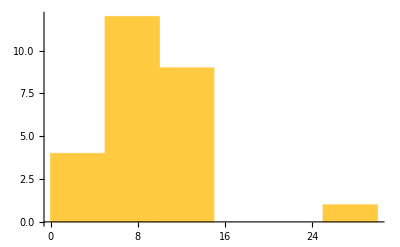

```mathematica
Map[Length,mainArtBaseTermWN[1985]]//Histogram
```

```mathematica
dcMean=Map[Length,mainArtBaseTermWN[1985]]//Mean//N
```

8.46154

```mathematica
dcMedian=Map[Length,mainArtBaseTermWN[1985]]//Median//N
```

8.

< 付与MeSH数が平均的なartのpos >

```mathematica
MSP[1985]=Nearest[Map[Length,mainArtBaseTermWN[1985]]->"Index",dcMedian,{All,dcMedian/2}]
```

{2,4,9,16,10,14,17,26,3,18,24,1,6,7,11,13,21,5,15,19,22}

```mathematica
Map[Length,mainArtBaseTermWN[1985]][[MSP[1985]]]
```

{8,8,8,8,9,7,7,9,10,10,6,5,5,11,5,11,11,12,12,12,4}

pubyearの条件は設定しない

< ruleの読み込み >

```mathematica
pubyearGather=Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearGatherSort.wl"];
PMIDtoPY=Association[Flatten[pubyearGather]];
```

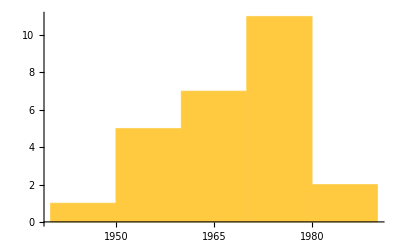

```mathematica
ToExpression[Map[PMIDtoPY,baseArt[1985]]]//Histogram
```

```mathematica
PySP[1985]=Table[n,{n,baseArt[1985]//Length}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

いずれの条件も満たすpos

```mathematica
(selectdPos[1985]=Intersection[MSP[1985],PySP[1985]])//Length
```

21

逆引きして確認する：

```mathematica
selecedPMID[1985]=baseArt[1985][[selectdPos[1985]]]
```

{14907713,5432063,1195397,13986422,5806584,13764136,6246368,942051,881736,13293190,4850204,4956917,265521,236308,271968,388439,388356,5962951,13641241,4887011,6159641}

```mathematica
ToExpression[Map[PMIDtoPY,selecedPMID[1985]]]//Sort
```

{1951,1956,1959,1961,1963,1965,1966,1969,1969,1970,1974,1975,1975,1976,1977,1977,1977,1979,1979,1980,1980}

```mathematica
mainArtBaseTermWN[1985][[selectdPos[1985]]]//Length
```

21

```mathematica
mainArtCitingTermWN[1985][[selectdPos[1985]]]//Length
```

21

```mathematica
meshCosDWN[mainArtBaseTermWN[1985][[selectdPos[1985]]][[1]],mainArtCitingTermWN[1985][[selectdPos[1985]]][[1]]]//N
```

0.966356

```mathematica
Inner[meshCosDWN,mainArtBaseTermWN[1985][[selectdPos[1985]]],mainArtCitingTermWN[1985][[selectdPos[1985]]],List]//N
```

{0.966356,0.840877,0.570673,0.745695,0.75662,0.700785,0.630057,0.942461,0.812514,0.823596,0.903754,0.535649,0.64295,0.580884,0.616457,0.674794,0.457805,0.516885,0.961667,0.758924,0.664094}

## 比較論文(25~26%)とそれを引用する論文

### 元Data

変数: topCitingCitedArt26Perc[YYYY, "citing rule"]

```mathematica
Q2Citingartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,Q2Citingartfiles];
```

### Q2論文のMeSHベクトル

```mathematica
Do[Q2ArtBaseTermWN[n]=Map[toWeighted[Cases[#,_String]]&,Map[Flatten,Map[PMIDtoMeSHDruleASC,Map[Union,Map[#[[2]]&,topCitingCitedArt26Perc[n, "citing rule"],{2}]],{2}]]],{n,1950,2020,5}]
```

```mathematica
Table[Q2ArtBaseTermWN[n]//Length,{n,1950,2020,5}]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

```mathematica
Q2ArtBaseTermWN[1955][[12]]
```

{Antibodies/6,Antigens/6,Humans/6,Kidney/6,Sulfur/6,(Sulfur Radioisotopes)/6}

### Q2論文を引用する(“citing”)論文集合のMeSHベクトル

```mathematica
Do[Q2ArtCitingTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC[#[[1]]]&,topCitingCitedArt26Perc[n, "citing rule"],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

```mathematica
Table[Q2ArtCitingTermWN[n]//Length,{n,1950,2020,5}]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

### Q2論文全てのciting-pivotの計算

```mathematica
(Q2citingPivotTbl=Table[Inner[meshCosDWN,Q2ArtBaseTermWN[n],Q2ArtCitingTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

15

## 比較論文(25~26%)とそれから引用される論文

### 元Data

変数: topCitedCitedArt26Perc[YYYY, "cited rule"]

```mathematica
Q2Citedartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitedCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitedCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitedCitedArt26Perc.save}

```mathematica
Map[Get,Q2Citedartfiles];
```

### Q2論文より引用される(“cited”)論文集合のMeSHベクトル

```mathematica
Do[Q2ArtCitedTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC,Map[#[[2]]&,topCitedCitedArt26Perc[n, "cited rule"],{2}],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定15391699⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

```mathematica
Table[Q2ArtCitedTermWN[n]//Length,{n,1950,2020,5}]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

```mathematica
Q2ArtCitedTermWN[2020]//Short
```

{{(1,2-Dipalmitoy…hatidylcholine)/13,(565 …)/3536,(«1»)/(«5»),«737»,(…g)/8,Xenopus/25},«25230»}

### Q2論文全てのcited-pivotの計算

```mathematica
Inner[meshCosDWN,Q2ArtBaseTermWN[1950],Q2ArtCitedTermWN[1950],List]//N
```

{Indeterminate,1.,0.,0.356256,Indeterminate,Indeterminate,Indeterminate,Indeterminate,1.,0.795876,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.741801,Indeterminate,1.,Indeterminate,Indeterminate,0.344438,Indeterminate,0.,0.,0.440103,Indeterminate,0.,1.,0.,0.765918,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,0.473765,0.490291,Indeterminate,Indeterminate,0.435633,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
(Q2citedPivotTbl=Table[Inner[meshCosDWN,Q2ArtBaseTermWN[n],Q2ArtCitedTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

15

### 通時的分析の対象となるQ2論文の選択

1985のtop26%論文（PMID）

```mathematica
(Q2baseArt[1985]=Map[Union[#][[1]]&,Map[#[[2]]&,topCitingCitedArt26Perc[1985, "citing rule"],{2}]])//Length
```

3668

付与されるMeSH数が平均的

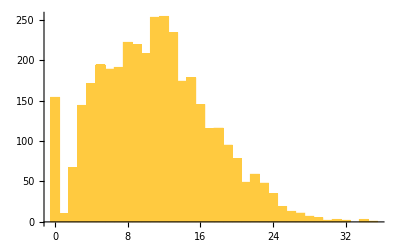

```mathematica
Map[Length,Q2ArtBaseTermWN[1985]]//Histogram
```

```mathematica
Q2dcMean=Map[Length,Q2ArtBaseTermWN[1985]]//Mean//N
```

10.9899

```mathematica
Q2dcMedian=Map[Length,Q2ArtBaseTermWN[1985]]//Median//N
```

11.

< 付与MeSH数が平均的なartのpos >

```mathematica
(Q2MSP[1985]=Nearest[Map[Length,Q2ArtBaseTermWN[1985]]->"Index",Q2dcMedian])//Length
```

253

pubyearの条件は設定しない

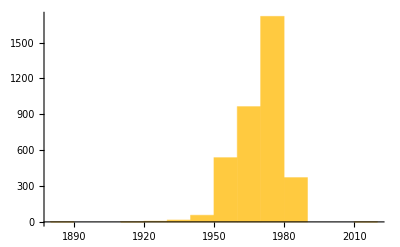

```mathematica
ToExpression[Map[PMIDtoPY,Q2baseArt[1985]]]//Histogram
```

```mathematica
(Q2PySP[1985]=Table[n,{n,Length[Q2baseArt[1985]]}])//Length
```

3668

いずれの条件も満たすpos

```mathematica
Intersection[Q2MSP[1985],Q2PySP[1985]]//Length
```

253

## 比較論文(50~51%)とそれを引用する論文

### 元Data

変数: topCitingCitedArt51Perc[YYYY, "citing rule"]

```mathematica
Q3Citingartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt51Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt51Perc.save}

```mathematica
Map[Get,Q3Citingartfiles];
```

### Q3論文のMeSHベクトル

```mathematica
Do[Q3ArtBaseTermWN[n]=Map[toWeighted[Cases[#,_String]]&,Map[Flatten,Map[PMIDtoMeSHDruleASC,Map[Union,Map[#[[2]]&,topCitingCitedArt51Perc[n, "citing rule"],{2}]],{2}]]],{n,1950,2020,5}]
```

```mathematica
Table[Q3ArtBaseTermWN[n]//Length,{n,1950,2020,5}]
```

{171,609,1581,2298,3476,5180,7022,8809,11951,15995,19764,26117,38410,53149,71777}

```mathematica
Q3ArtBaseTermWN[1955][[12]]
```

{Orthomyxoviridae}

### Q3論文を引用する(“citing”)論文集合のMeSHベクトル

```mathematica
Do[Q3ArtCitingTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC[#[[1]]]&,topCitingCitedArt51Perc[n, "citing rule"],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

```mathematica
Table[Q3ArtCitingTermWN[n]//Length,{n,1950,2020,5}]
```

{171,609,1581,2298,3476,5180,7022,8809,11951,15995,19764,26117,38410,53149,71777}

```mathematica
Q3ArtCitingTermWN[2020][[1]]
```

{Acetylcholinesterase/24,(Adenosine A2 Receptor Antagonists)/11,(5 Adolescent)/36,(49 Adult)/176,Aerosols/18,(5 Aged)/48,Agriculture/16,Alkaloids/4,(alpha7 Nicotinic Acetylcholine Receptor)/7,(Alzheimer Disease)/4,(745 Animals)/693,(259 Antiparkinson Agents)/792,(15 Astrocytes)/56,Atherosclerosis/8,Benzazepines/16,(23 Brain)/144,Butyrylcholinesterase/24,Calcineurin/14,(Calcium-Calmodulin-Dependent Protein Kinase Type 2)/14,Calmodulin/14,(Carcinoma, Ovarian Epithelial)/13,(Cardiovascular System)/8,(Cell Death)/11,(359 Cell Line, Tumor)/1287,(29 Cell Proliferation)/208,(Cells, Cultured)/7,(Cell Shape)/16,(20 Cell Survival)/99,(Cellular Senescence)/8,(Central Nervous System Diseases)/8,(Cerebral Cortex)/7,Cholinesterases/16,(Cognitive Dysfunction)/9,(Complementary Therapies)/9,(Computational Biology)/7,(Contrast Sensitivity)/11,(3 Cotinine)/16,Cytoprotection/9,(Depressive Disorder)/9,(Disease Models, Animal)/8,(Disease Progression)/4,(27 Dopamine)/176,(Dopamine Agonists)/16,(15 Dopaminergic Neurons)/112,(Dose-Response Relationship, Drug)/9,(Down-Regulation)/14,(Drosophila melanogaster)/14,(Drosophila Proteins)/14,(19 Dyskinesia, Drug-Induced)/88,(eIF-2 Kinase)/14,(Electronic Nicotine Delivery Systems)/18,(Emigrants and Immigrants)/24,(Endoplasmic Reticulum)/14,(Endoplasmic Reticulum Stress)/14,(Eukaryotic Initiation Factor-2)/14,(Excitatory Amino Acid Antagonists)/11,Farmers/16,(2729 Female)/10296,(Free Radicals)/18,(GTP Phosphohydrolases)/8,(Heat-Shock Response)/14,Hippocampus/14,(5 Hispanic or Latino)/48,(72803 Humans)/36036,Hypothyroidism/14,(Image Processing, Computer-Assisted)/24,Imidazoles/13,Indoles/16,(Induced Pluripotent Stem Cells)/16,Inflammation/8,Iron/9,Levodopa/8,Lipids/12,Liver/12,Locomotion/14,(Magnetic Resonance Imaging)/24,(519 Male)/1232,Manganese/9,(Membrane Transport Modulators)/11,Mesencephalon/16,(Metals, Heavy)/18,Mice/7,Microglia/7,(103 Middle Aged)/528,Mitochondria/8,(Mitochondrial Dynamics)/8,(Models, Biological)/4,(Models, Statistical)/24,(Molecular Targeted Therapy)/7,(Morris Water Maze Test)/14,(Motor Activity)/11,Nanoparticles/18,(Neural Pathways)/24,(11 Neurodegenerative Diseases)/28,(Neuronal Plasticity)/16,Neurons/11,Neuroprotection/16,(239 Neuroprotective Agents)/693,(Neurotoxicity Syndromes)/18,(Neurotransmitter Agents)/8,Nicotiana/6,(49391 Nicotine)/48048,(North Carolina)/16,Obesity/8,(5 Occupational Exposure)/48,(Ovarian Neoplasms)/13,(Oxidative Stress)/11,Oxygen/24,(p38 Mitogen-Activated Protein Kinases)/13,(161 Parkinson Disease)/198,(Parkinson Disease, Secondary)/11,(5 Pesticides)/48,(307 Phosphorylation)/1456,Phytochemicals/4,(Plant Leaves)/6,(Plant Proteins)/6,(Plants, Genetically Modified)/6,Pregnancy/18,Probability/24,(Protective Agents)/4,(Protein Kinase C)/14,(Public Health)/18,Pyridines/13,Quinpirole/16,(Rats, Wistar)/14,(Reactive Oxygen Species)/11,(Receptors, Dopamine D2)/16,(Receptors, Dopamine D3)/16,(Receptors, Neurotransmitter)/8,(Receptors, Nicotinic)/13,(Regression Analysis)/24,Rest/24,(Retrospective Studies)/24,Rotenone/11,Saliva/12,(Serotonin Antagonists)/11,(20 Signal Transduction)/91,(Sleep Wake Disorders)/9,(29 Smokers)/198,(29 Smoking)/198,(Smoking Cessation)/11,(Space Perception)/11,(Spatial Memory)/14,(Task Performance and Analysis)/14,(Tobacco, Smokeless)/12,(5 Tobacco Use)/24,(Trace Elements)/18,(Transcription Factors)/6,(Transients and Migrants)/16,(Treatment Outcome)/9,Vaping/18,(Vision, Ocular)/11,(Young Adult)/12}

### Q3論文全てのciting-pivotの計算

```mathematica
(Q3citingPivotTbl=Table[Inner[meshCosDWN,Q3ArtBaseTermWN[n],Q3ArtCitingTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

15

## 比較論文(50~51%)とそれから引用される論文

### 元Data

変数: topCitedCitedArt51Perc[YYYY, "cited rule"]

```mathematica
Q3Citedartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitedCitedArt51Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitedCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitedCitedArt51Perc.save}

```mathematica
Map[Get,Q3Citedartfiles];
```

### Q3論文より引用される(“cited”)論文集合のMeSHベクトル

```mathematica
Do[Q3ArtCitedTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC,Map[#[[2]]&,topCitedCitedArt51Perc[n, "cited rule"],{2}],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定15435524⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

```mathematica
Table[Q3ArtCitedTermWN[n]//Length,{n,1950,2020,5}]
```

{171,609,1581,2298,3476,5180,7022,8809,11951,15995,19764,26117,38410,53149,71777}

```mathematica
Q3ArtCitedTermWN[2020]//Short
```

{{(5657 1-Methyl-4…ropyridine)/12540,(3…id)/19,«661»,…/19,(Zinc T…rter 8)/21},«71775»,0}

### Q3論文全てのcited-pivotの計算

```mathematica
Inner[meshCosDWN,Q3ArtBaseTermWN[1950],Q3ArtCitedTermWN[1950],List]//N
```

{Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.5,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.5,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
(Q3citedPivotTbl=Table[Inner[meshCosDWN,Q3ArtBaseTermWN[n],Q3ArtCitedTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

Keys::invrl: 引数Association[weightCount/@{2,Streptomycin}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2.,Streptomycin}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2,Tuberculin}]は有効なAssociationでも規則のリストでもありません．

General::stop: この計算中に，Keys::invrlのこれ以上の出力は表示されません．

15

```mathematica
Map[Head,(Q3citedPivotTbl//Flatten)]//Tally
```

{{Symbol,173875},{Real,92432},{Plus,2}}

### 通時的分析の対象となるQ3論文の選択

1985のtop51%論文（PMID）

```mathematica
(Q3baseArt[1985]=Map[Union[#][[1]]&,Map[#[[2]]&,topCitingCitedArt51Perc[1985, "citing rule"],{2}]])//Length
```

8809

付与されるMeSH数が平均的

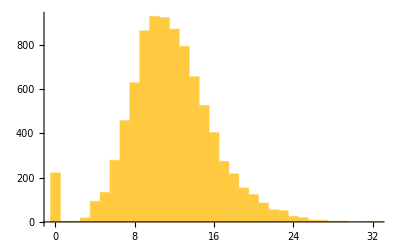

```mathematica
Map[Length,Q3ArtBaseTermWN[1985]]//Histogram
```

```mathematica
Q3dcMean=Map[Length,Q3ArtBaseTermWN[1985]]//Mean//N
```

11.5928

```mathematica
Q3dcMedian=Map[Length,Q3ArtBaseTermWN[1985]]//Median//N
```

11.

< 付与MeSH数が平均的なartのpos >

```mathematica
(Q3MSP[1985]=Nearest[Map[Length,Q3ArtBaseTermWN[1985]]->"Index",Q3dcMedian])//Length
```

922

pubyearの条件は設定しない

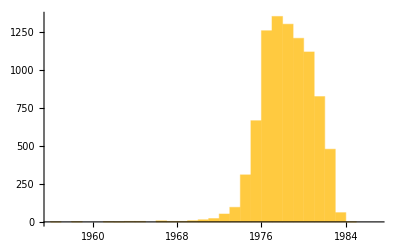

```mathematica
ToExpression[Map[PMIDtoPY,Q3baseArt[1985]]]//Histogram
```

```mathematica
Q3PySP[1985]=Table[n,{n,Length[Q3baseArt[1985]]}];
```

いずれの条件も満たすpos

```mathematica
Intersection[Q3MSP[1985],Q3PySP[1985]]//Length
```

922

## 比較論文(75~76%)とそれを引用する論文

### 元Data

変数: topCitingCitedArt76Perc[YYYY, "citing rule"]

```mathematica
Q4Citingartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt76Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt76Perc.save}

```mathematica
Map[Get,Q4Citingartfiles];
```

### Q4論文のMeSHベクトル

```mathematica
Do[Q4ArtBaseTermWN[n]=Map[toWeighted[Cases[#,_String]]&,Map[Flatten,Map[PMIDtoMeSHDruleASC,Map[Union,Map[#[[2]]&,topCitingCitedArt76Perc[n, "citing rule"],{2}]],{2}]]],{n,1950,2020,5}]
```

```mathematica
Table[Q4ArtBaseTermWN[n]//Length,{n,1950,2020,5}]
```

{339,1825,2371,4596,8690,10359,17021,24736,29877,44166,47524,66758,102058,138818,190452}

### Q4論文を引用する(“citing”)論文集合のMeSHベクトル

```mathematica
Do[Q4ArtCitingTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC[#[[1]]]&,topCitingCitedArt76Perc[n, "citing rule"],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

```mathematica
Table[Q4ArtCitingTermWN[n]//Length,{n,1950,2020,5}]
```

{339,1825,2371,4596,8690,10359,17021,24736,29877,44166,47524,66758,102058,138818,190452}

```mathematica
Q4ArtCitingTermWN[2020][[1]]
```

{(Actin Cytoskeleton)/5,(Actin-Related Protein 2-3 Complex)/5,(393 Actins)/1330,(30 Adaptor Proteins, Signal Transducing)/221,Adult/11,Aging/11,(1982143 Animals)/3233230,(Animals, Genetically Modified)/11,Astrocytes/11,(CA1 Region, Hippocampal)/19,(CA2 Region, Hippocampal)/19,Cattle/10,(Cell Cycle)/11,(Cell Differentiation)/11,(Cell Line, Tumor)/10,(Cell Movement)/10,(36 Cells, Cultured)/323,(Cell Surface Extensions)/10,(Cell Survival)/19,(Cyclin A2)/11,(Cytoplasmic Granules)/11,(Dendritic Spines)/19,(Drosophila melanogaster)/17,(Drosophila Proteins)/17,(Embryonic Stem Cells)/11,(Epistasis, Genetic)/17,(Excitatory Postsynaptic Potentials)/13,(Exome Sequencing)/11,Fear/13,(24 Female)/143,(Fragile X Mental Retardation Protein)/17,(Gene Knockout Techniques)/17,(Gene Silencing)/17,Glycine/19,(Green Fluorescent Proteins)/19,Heterozygote/11,Hippocampus/11,(Homeodomain Proteins)/11,Homeostasis/11,(3224 Humans)/6545,(Inheritance Patterns)/13,(Intellectual Disability)/11,Learning/19,(Long-Term Potentiation)/19,(24 Male)/143,Memory/19,(599 Mice)/2717,(30 Mice, Inbred C57BL)/221,(Mice, Knockout)/13,(30 Mice, Transgenic)/209,(Microfilament Proteins)/10,(Microscopy, Electron)/10,(Microscopy, Fluorescence)/10,(Multiprotein Complexes)/17,Mutation/11,(30 Nerve Tissue Proteins)/221,(Neuromuscular Depolarizing Agents)/19,(Neuronal Plasticity)/19,(28 Neurons)/187,(Olfactory Bulb)/17,(Patch-Clamp Techniques)/19,Polymerization/10,(Potassium Chloride)/19,(Prader-Willi Syndrome)/13,(Protein Kinase C)/19,(Protein Structure, Tertiary)/10,Pseudopodia/10,(Pyramidal Cells)/11,Respiration/11,(RNA, Messenger)/17,(RNA, Ribosomal)/11,Seizures/11,Sleep/11,(Spinal Diseases)/7,Spine/7,(Stress Fibers)/7,(311 Synapses)/1001,(Transcription Factors)/11,(327 Wiskott-Aldrich Syndrome Protein Family)/935,(Young Adult)/11}

### Q4論文全てのciting-pivotの計算

```mathematica
(Q4citingPivotTbl=Table[Inner[meshCosDWN,Q4ArtBaseTermWN[n],Q4ArtCitingTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

Keys::invrl: 引数Association[weightCount/@{2,Bacteria}]は有効なAssociationでも規則のリストでもありません．

General::stop: この計算中に，Keys::invrlのこれ以上の出力は表示されません．

15

## 比較論文(75~76%)とそれから引用される論文

### 元Data

変数: topCitedCitedArt76Perc[YYYY, "cited rule"]

```mathematica
Q4Citedartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitedCitedArt76Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitedCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitedCitedArt76Perc.save}

```mathematica
Map[Get,Q4Citedartfiles];
```

### Q4論文より引用される(“cited”)論文集合のMeSHベクトル

```mathematica
Do[Q4ArtCitedTermWN[n]=MapApply[List,MapApply[Plus,Map[Flatten,Map[toWeighted,DeleteCases[Map[PMIDtoMeSHDruleASC,Map[#[[2]]&,topCitedCitedArt76Perc[n, "cited rule"],{2}],{2}],_Missing,{2}],{2}]]]],{n,1950,2020,5}]
```

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定16993675⟦2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定KeyAbsent⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

```mathematica
Table[Q4ArtCitedTermWN[n]//Length,{n,1950,2020,5}]
```

{339,1825,2371,4596,8690,10359,17021,24736,29877,44166,47524,66758,102058,138818,190452}

```mathematica
Q4ArtCitedTermWN[2020][[2]]
```

{(1565 Adult)/3276,(11 Aged)/84,(Aged, 80 and over)/12,(24 Algorithms)/143,(169 Animals)/252,Anisotropy/11,(Anti-Inflammatory Agents, Non-Steroidal)/12,Archives/9,Aspirin/12,(Basal Ganglia)/11,(Bayes Theorem)/9,(Biological Evolution)/5,Biomarkers/8,(Biomedical Research)/9,(1849 Brain)/2520,(48847 Brain Mapping)/72072,(Cardiovascular Diseases)/12,(Case-Control Studies)/12,Cerebellum/7,(Cerebral Cortex)/9,(2 Cognition)/21,(Computer Simulation)/11,(Computer Systems)/9,(Database Management Systems)/9,(17 Databases, Factual)/72,(Databases, Genetic)/5,(32 Data Interpretation, Statistical)/231,(Demyelinating Diseases)/8,(25 Diagnostic Imaging)/72,Diffusion/5,(Diffusion Magnetic Resonance Imaging)/11,(Discriminant Analysis)/11,(Disease Progression)/21,(Echo-Planar Imaging)/9,(Executive Function)/21,(13385 Female)/18018,Genome/5,(Genotyping Techniques)/21,(Gyrus Cinguli)/21,(Health Behavior)/12,Heterozygote/21,Hippocampus/8,(597757 Humans)/360360,(Huntingtin Protein)/21,(206 Huntington Disease)/693,(24 Image Enhancement)/143,(2 Image Interpretation, Computer-Assisted)/11,(29929 Image Processing, Computer-Assisted)/36036,(Imaging, Three-Dimensional)/13,(Information Dissemination)/9,(Information Storage and Retrieval)/9,(Information Systems)/9,(14 Internet)/45,Iron/9,Laboratories/8,(Linear Models)/13,(Local Area Networks)/11,(10 Longitudinal Studies)/63,(3494 Magnetic Resonance Imaging)/3003,Magnetics/11,(35779 Male)/36036,(Medical Records Systems, Computerized)/9,(Mental Disorders)/21,(11 Mice)/28,(11 Mice, Inbred C57BL)/28,Microcomputers/11,(283 Middle Aged)/693,(Models, Biological)/11,(5 Models, Neurological)/18,(14 Models, Statistical)/45,(Motor Activity)/21,(17 Myelin Sheath)/72,(National Institutes of Health (U.S.))/9,Neostriatum/21,(Nerve Net)/12,(Nerve Tissue Proteins)/21,(Nervous System Diseases)/9,(Neural Networks, Computer)/6,(26 Neural Pathways)/105,(Neurodegenerative Diseases)/8,Neuroimaging/9,(2 Neuropsychological Tests)/21,Neuroradiography/9,(Nonlinear Dynamics)/11,Oxygen/21,(Phantoms, Imaging)/11,(Pilot Projects)/12,(Prefrontal Cortex)/21,(Primary Prevention)/12,(Promoter Regions, Genetic)/5,(Psychomotor Performance)/21,(Quantum Theory)/6,(Randomized Controlled Trials as Topic)/12,(Reaction Time)/21,(Regression Analysis)/21,(439 Reproducibility of Results)/1144,Rest/21,(ROC Curve)/12,Schizophrenia/12,(Search Engine)/9,(431 Sensitivity and Specificity)/1716,(Signal Processing, Computer-Assisted)/21,(14 Software)/33,(Systems Integration)/9,(2 United States)/9,(User-Computer Interface)/9}

### Q4論文全てのcited-pivotの計算

```mathematica
Inner[meshCosDWN,Q4ArtBaseTermWN[1950],Q4ArtCitedTermWN[1950],List]//N
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.612702,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.666667,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
(Q4citedPivotTbl=Table[Inner[meshCosDWN,Q4ArtBaseTermWN[n],Q4ArtCitedTermWN[n],List]//N,{n,1950,2020,5}])//Length
```

Keys::invrl: 引数Association[weightCount/@{2,Dicumarol}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2,Brucella}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2.,Dicumarol}]は有効なAssociationでも規則のリストでもありません．

General::stop: この計算中に，Keys::invrlのこれ以上の出力は表示されません．

15

```mathematica
Map[Head,(Q4citedPivotTbl//Flatten)]//Tally
```

{{Symbol,485735},{Real,203851},{Plus,4}}

### 通時的分析の対象となるQ4論文の選択

1985のtop51%論文（PMID）

```mathematica
(Q4baseArt[1985]=Map[Union[#][[1]]&,Map[#[[2]]&,topCitingCitedArt76Perc[1985, "citing rule"],{2}]])//Length
```

24736

付与されるMeSH数が平均的

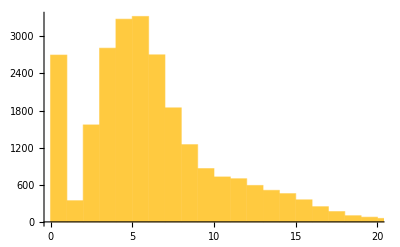

```mathematica
Map[Length,Q4ArtBaseTermWN[1985]]//Histogram
```

```mathematica
Q4dcMean=Map[Length,Q4ArtBaseTermWN[1985]]//Mean//N
```

5.73783

```mathematica
Q4dcMedian=Map[Length,Q4ArtBaseTermWN[1985]]//Median//N
```

5.

< 付与MeSH数が平均的なartのpos >

```mathematica
(Q4MSP[1985]=Nearest[Map[Length,Q4ArtBaseTermWN[1985]]->"Index",Q4dcMedian])//Length
```

3321

pubyearの条件は設定しない

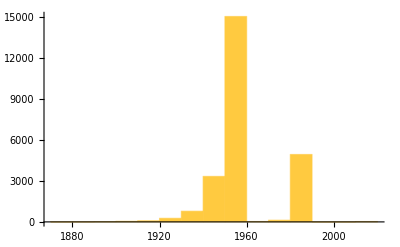

```mathematica
ToExpression[Map[PMIDtoPY,Q4baseArt[1985]]]//Histogram
```

```mathematica
Q4PySP[1985]=Table[n,{n,Length[Q4baseArt[1985]]}];
```

いずれの条件も満たすpos

```mathematica
Intersection[Q4MSP[1985],Q4PySP[1985]]//Length
```

3321

## Save

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/"<>"mesh-pivot-tables.save",{citingPivotTbl,citedPivotTbl,Q2citingPivotTbl,Q2citingPivotTbl,Q3citingPivotTbl,Q3citedPivotTbl,Q4citingPivotTbl,Q4citedPivotTbl}]*)
```

## Plot: 代表論文群とそれを引用する論文

```mathematica
citingPivotTbl//Length
Q2citingPivotTbl//Length
Q3citingPivotTbl//Length
Q4citingPivotTbl//Length
```

14

15

15

15

1950 世代は除外する。

```mathematica
ccitingPivotTbl=citingPivotTbl;
cQ2citingPivotTbl=Drop[Q2citingPivotTbl,1];
cQ3citingPivotTbl=Drop[Q3citingPivotTbl,1];
cQ4citingPivotTbl=Drop[Q4citingPivotTbl,1];
```

さらにRealを選択してtestableにする。

```mathematica
tcitingPivotTbl=Map[Cases[#,_Real]&,ccitingPivotTbl];
tQ2citingPivotTbl=Map[Cases[#,_Real]&,cQ2citingPivotTbl];
tQ3citingPivotTbl=Map[Cases[#,_Real]&,cQ3citingPivotTbl];
tQ4citingPivotTbl=Map[Cases[#,_Real]&,cQ4citingPivotTbl];
```

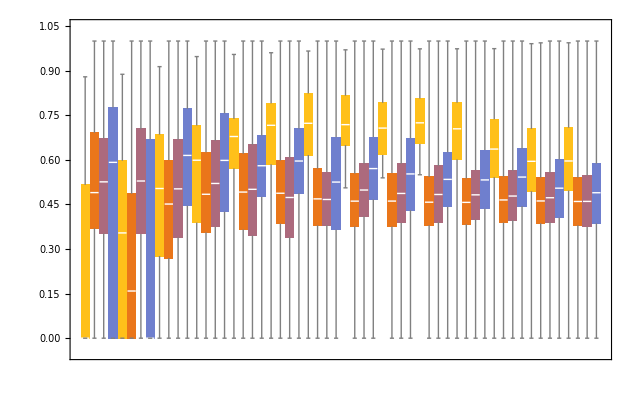

```mathematica
BoxWhiskerChart[Table[{tcitingPivotTbl[[n]],tQ2citingPivotTbl[[n]],tQ3citingPivotTbl[[n]],tQ4citingPivotTbl[[n]]},{n,1,14}],"Median"]
```

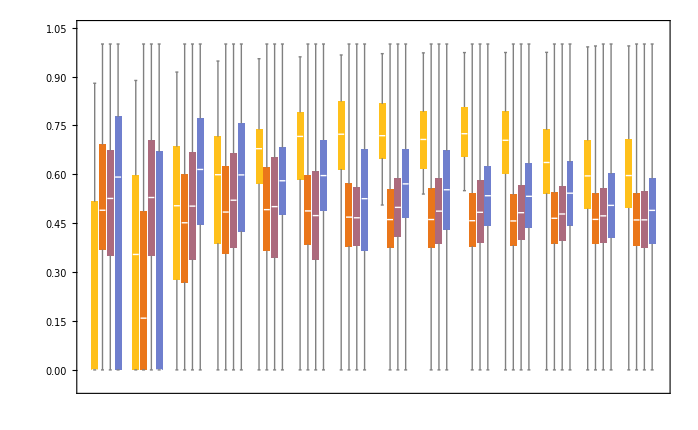

```mathematica
BoxWhiskerChart[Table[{tcitingPivotTbl[[n]],tQ2citingPivotTbl[[n]],tQ3citingPivotTbl[[n]],tQ4citingPivotTbl[[n]]},{n,1,14}],"Median",ChartLayout->"Grouped",BarSpacing->{0.3,1.5}]
```

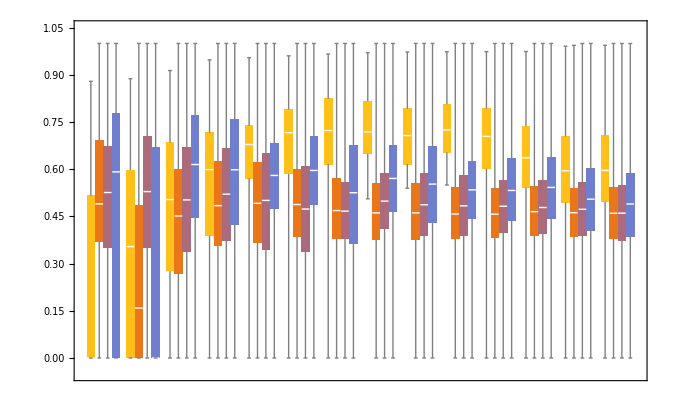

```mathematica
BoxWhiskerChart[Table[{tcitingPivotTbl[[n]],tQ2citingPivotTbl[[n]],tQ3citingPivotTbl[[n]],tQ4citingPivotTbl[[n]]},{n,1,14}],"Median",ChartLayout->"Grouped",BarSpacing->{0.1,0.8}]
```

## 検定

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/"<>"mesh-pivot-tables.save"];
```

Keys::invrl: 引数Association[weightCount/@{2.,Streptomycin}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2.,Tuberculin}]は有効なAssociationでも規則のリストでもありません．

Keys::invrl: 引数Association[weightCount/@{2.,Rhizobium}]は有効なAssociationでも規則のリストでもありません．

General::stop: この計算中に，Keys::invrlのこれ以上の出力は表示されません．

## 代表論文をcitingするテーマ

```mathematica
citingPivotTbl//Length
Q2citingPivotTbl//Length
Q3citingPivotTbl//Length
Q4citingPivotTbl//Length
```

14

15

15

15

1950 世代は除外する。

```mathematica
ccitingPivotTbl=citingPivotTbl;
cQ2citingPivotTbl=Drop[Q2citingPivotTbl,1];
cQ3citingPivotTbl=Drop[Q3citingPivotTbl,1];
cQ4citingPivotTbl=Drop[Q4citingPivotTbl,1];
```

さらにRealを選択してtestableにする。

```mathematica
tcitingPivotTbl=Map[Cases[#,_Real]&,ccitingPivotTbl];
tQ2citingPivotTbl=Map[Cases[#,_Real]&,cQ2citingPivotTbl];
tQ3citingPivotTbl=Map[Cases[#,_Real]&,cQ3citingPivotTbl];
tQ4citingPivotTbl=Map[Cases[#,_Real]&,cQ4citingPivotTbl];
```

### 時系列（近接年）検定

#### top

```mathematica
ccitingPivotTbl//Length
```

14

```mathematica
mannwhitneyYearP["top"]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Partition[tcitingPivotTbl,2,1]]
```

{0.1494,0.0692,0.239,0.0324,0.3274,0.7206,0.754,0.7748,0.5842,0.3542,0.001,0.0092,0.5926}

#### Q2

```mathematica
mannwhitneyYearP["Q2"]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Partition[tQ2citingPivotTbl,2,1]]
```

{0.,0.,0.,0.6398,0.759,0.,0.0078,0.8698,0.0864,0.8984,0.,0.0076,0.0054}

#### Q3

```mathematica
mannwhitneyYearP["Q3"]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Partition[tQ3citingPivotTbl,2,1]]
```

{0.7188,0.0042,0.0044,0.,0.,0.3896,0.,0.,0.1434,0.21,0.0032,0.,0.}

#### Q4

```mathematica
mannwhitneyYearP["Q4"]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Partition[tQ4citingPivotTbl,2,1]]
```

{0.,0.,0.0028,0.,0.,0.,0.,0.,0.,0.85,0.,0.,0.}

#### Save

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/exec_command/element/mesh/"<>"year-pivot-test.save",mannwhitneyYearP]*)
```

#### Show

```mathematica
NumberForm[TableForm[{mannwhitneyYearP["top"],mannwhitneyYearP["Q2"],mannwhitneyYearP["Q3"],mannwhitneyYearP["Q4"]}],{tdigit,tdigit}]
```

0.149 | 0.069 | 0.239 | 0.032 | 0.327 | 0.721 | 0.754 | 0.775 | 0.584 | 0.354 | 0.001 | 0.009 | 0.593
0.000 | 0.000 | 0.000 | 0.640 | 0.759 | 0.000 | 0.008 | 0.870 | 0.086 | 0.898 | 0.000 | 0.008 | 0.005
0.719 | 0.004 | 0.004 | 0.000 | 0.000 | 0.390 | 0.000 | 0.000 | 0.143 | 0.210 | 0.003 | 0.000 | 0.000
0.000 | 0.000 | 0.003 | 0.000 | 0.000 | 0.000 | 0.000 | 0.000 | 0.000 | 0.850 | 0.000 | 0.000 | 0.000

### グループ間の検定

#### testの確認

```mathematica
l1={1,2,3}
l2={2,3,4,8}
```

{1,2,3}

{2,3,4,8}

```mathematica
MannWhitneyTest[{l1,l2}]
```

0.114286

p - valueを返している。

```mathematica
MannWhitneyTest[{l1,l2},0,"PValue"]
```

0.114286

```mathematica
MannWhitneyTest[{l1,l2},0,Method->"Permutation"]
```

0.2946

置換テストを行う。

```mathematica
MannWhitneyTest[{l1,l2},0,"PValue",Method->"Permutation"]
```

0.2894

#### サイズの確認

```mathematica
Map[Length,tcitingPivotTbl]
Map[Length,tQ2citingPivotTbl]
Map[Length,tQ3citingPivotTbl]
Map[Length,tQ4citingPivotTbl]
```

{30,46,50,38,33,32,26,19,22,33,66,192,315,336}

{302,590,932,1443,2051,2826,3653,4634,5913,7225,9778,14654,19457,25229}

{588,1580,2264,3442,5148,6973,8674,11951,15727,19528,26117,38382,53140,71711}

{1575,1570,4457,8564,10188,16755,24326,29877,43033,47524,66755,101639,138189,189394}

```mathematica
tdigit=3
```

3

#### 1955

```mathematica
Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[1]],tQ2citingPivotTbl[[1]],tQ3citingPivotTbl[[1]],tQ4citingPivotTbl[[1]]},{tcitingPivotTbl[[1]],tQ2citingPivotTbl[[1]],tQ3citingPivotTbl[[1]],tQ4citingPivotTbl[[1]]},1],{2}]
```

{{0.9958,0.,0.,0.0002},{0.,0.992,0.7222,0.5402},{0.,0.7382,0.9952,0.657},{0.,0.5712,0.6734,0.9908}}

```mathematica
NumberForm[(mannwhitneyP[1955]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[1]],tQ2citingPivotTbl[[1]],tQ3citingPivotTbl[[1]],tQ4citingPivotTbl[[1]]},{tcitingPivotTbl[[1]],tQ2citingPivotTbl[[1]],tQ3citingPivotTbl[[1]],tQ4citingPivotTbl[[1]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

1.000 | 0.000 | 0.000 | 0.000
0.000 | 0.995 | 0.727 | 0.546
0.000 | 0.708 | 0.993 | 0.656
0.000 | 0.548 | 0.677 | 1.000

```mathematica
mannwhitneyP[1955]
```

{{0.9998,0.,0.,0.0004},{0.,0.9952,0.7272,0.5458},{0.,0.7084,0.9926,0.6564},{0.,0.5484,0.6768,0.9996}}

#### 1960

```mathematica
NumberForm[(mannwhitneyP[1960]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[2]],tQ2citingPivotTbl[[2]],tQ3citingPivotTbl[[2]],tQ4citingPivotTbl[[2]]},{tcitingPivotTbl[[2]],tQ2citingPivotTbl[[2]],tQ3citingPivotTbl[[2]],tQ4citingPivotTbl[[2]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.999 | 0.070 | 0.000 | 0.324
0.081 | 0.995 | 0.000 | 0.124
0.000 | 0.000 | 0.991 | 0.000
0.327 | 0.114 | 0.000 | 0.996

#### 1965

```mathematica
NumberForm[(mannwhitneyP[1965]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[3]],tQ2citingPivotTbl[[3]],tQ3citingPivotTbl[[3]],tQ4citingPivotTbl[[3]]},{tcitingPivotTbl[[3]],tQ2citingPivotTbl[[3]],tQ3citingPivotTbl[[3]],tQ4citingPivotTbl[[3]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.973 | 0.364 | 0.454 | 0.001
0.361 | 0.999 | 0.000 | 0.000
0.460 | 0.000 | 0.992 | 0.000
0.000 | 0.000 | 0.000 | 0.999

#### 1970

```mathematica
NumberForm[(mannwhitneyP[1970]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[4]],tQ2citingPivotTbl[[4]],tQ3citingPivotTbl[[4]],tQ4citingPivotTbl[[4]]},{tcitingPivotTbl[[4]],tQ2citingPivotTbl[[4]],tQ3citingPivotTbl[[4]],tQ4citingPivotTbl[[4]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.988 | 0.084 | 0.380 | 0.294
0.096 | 0.996 | 0.000 | 0.000
0.372 | 0.000 | 0.995 | 0.000
0.297 | 0.000 | 0.000 | 0.971

#### 1975

```mathematica
NumberForm[(mannwhitneyP[1975]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[5]],tQ2citingPivotTbl[[5]],tQ3citingPivotTbl[[5]],tQ4citingPivotTbl[[5]]},{tcitingPivotTbl[[5]],tQ2citingPivotTbl[[5]],tQ3citingPivotTbl[[5]],tQ4citingPivotTbl[[5]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.988 | 0.000 | 0.000 | 0.002
0.000 | 0.998 | 0.119 | 0.000
0.000 | 0.128 | 0.994 | 0.000
0.003 | 0.000 | 0.000 | 0.988

#### 1980

```mathematica
NumberForm[(mannwhitneyP[1980]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[6]],tQ2citingPivotTbl[[6]],tQ3citingPivotTbl[[6]],tQ4citingPivotTbl[[6]]},{tcitingPivotTbl[[6]],tQ2citingPivotTbl[[6]],tQ3citingPivotTbl[[6]],tQ4citingPivotTbl[[6]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.988 | 0.000 | 0.000 | 0.001
0.000 | 0.994 | 0.000 | 0.000
0.000 | 0.000 | 0.989 | 0.000
0.000 | 0.000 | 0.000 | 0.991

#### 1985

```mathematica
NumberForm[(mannwhitneyP[1985]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[7]],tQ2citingPivotTbl[[7]],tQ3citingPivotTbl[[7]],tQ4citingPivotTbl[[7]]},{tcitingPivotTbl[[7]],tQ2citingPivotTbl[[7]],tQ3citingPivotTbl[[7]],tQ4citingPivotTbl[[7]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.986 | 0.000 | 0.000 | 0.000
0.000 | 0.993 | 0.284 | 0.000
0.000 | 0.296 | 0.990 | 0.000
0.000 | 0.000 | 0.000 | 0.988

#### 1990

```mathematica
NumberForm[(mannwhitneyP[1990]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[8]],tQ2citingPivotTbl[[8]],tQ3citingPivotTbl[[8]],tQ4citingPivotTbl[[8]]},{tcitingPivotTbl[[8]],tQ2citingPivotTbl[[8]],tQ3citingPivotTbl[[8]],tQ4citingPivotTbl[[8]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.972 | 0.000 | 0.000 | 0.000
0.000 | 0.997 | 0.000 | 0.000
0.000 | 0.000 | 0.991 | 0.000
0.000 | 0.000 | 0.000 | 0.986

#### 1995

```mathematica
NumberForm[(mannwhitneyP[1995]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[9]],tQ2citingPivotTbl[[9]],tQ3citingPivotTbl[[9]],tQ4citingPivotTbl[[9]]},{tcitingPivotTbl[[9]],tQ2citingPivotTbl[[9]],tQ3citingPivotTbl[[9]],tQ4citingPivotTbl[[9]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.987 | 0.000 | 0.000 | 0.000
0.000 | 0.999 | 0.000 | 0.000
0.000 | 0.000 | 0.986 | 0.000
0.000 | 0.000 | 0.000 | 0.994

#### 2000

```mathematica
NumberForm[(mannwhitneyP[2000]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[10]],tQ2citingPivotTbl[[10]],tQ3citingPivotTbl[[10]],tQ4citingPivotTbl[[10]]},{tcitingPivotTbl[[10]],tQ2citingPivotTbl[[10]],tQ3citingPivotTbl[[10]],tQ4citingPivotTbl[[10]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.998 | 0.000 | 0.000 | 0.000
0.000 | 0.994 | 0.000 | 0.000
0.000 | 0.000 | 0.987 | 0.000
0.000 | 0.000 | 0.000 | 0.991

#### 2005

```mathematica
NumberForm[(mannwhitneyP[2005]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[11]],tQ2citingPivotTbl[[11]],tQ3citingPivotTbl[[11]],tQ4citingPivotTbl[[11]]},{tcitingPivotTbl[[11]],tQ2citingPivotTbl[[11]],tQ3citingPivotTbl[[11]],tQ4citingPivotTbl[[11]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.992 | 0.000 | 0.000 | 0.000
0.000 | 0.991 | 0.000 | 0.000
0.000 | 0.000 | 0.993 | 0.000
0.000 | 0.000 | 0.000 | 0.996

#### 2010

```mathematica
NumberForm[(mannwhitneyP[2010]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[12]],tQ2citingPivotTbl[[12]],tQ3citingPivotTbl[[12]],tQ4citingPivotTbl[[12]]},{tcitingPivotTbl[[12]],tQ2citingPivotTbl[[12]],tQ3citingPivotTbl[[12]],tQ4citingPivotTbl[[12]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.996 | 0.000 | 0.000 | 0.000
0.000 | 0.995 | 0.000 | 0.000
0.000 | 0.000 | 0.994 | 0.000
0.000 | 0.000 | 0.000 | 0.983

#### 2015

```mathematica
NumberForm[(mannwhitneyP[2015]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[13]],tQ2citingPivotTbl[[13]],tQ3citingPivotTbl[[13]],tQ4citingPivotTbl[[13]]},{tcitingPivotTbl[[13]],tQ2citingPivotTbl[[13]],tQ3citingPivotTbl[[13]],tQ4citingPivotTbl[[13]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.995 | 0.000 | 0.000 | 0.000
0.000 | 0.994 | 0.000 | 0.000
0.000 | 0.000 | 0.988 | 0.000
0.000 | 0.000 | 0.000 | 0.981

#### 2020

```mathematica
NumberForm[(mannwhitneyP[2020]=Map[MannWhitneyTest[#,0,Method->"Permutation"]&,Outer[List,{tcitingPivotTbl[[14]],tQ2citingPivotTbl[[14]],tQ3citingPivotTbl[[14]],tQ4citingPivotTbl[[14]]},{tcitingPivotTbl[[14]],tQ2citingPivotTbl[[14]],tQ3citingPivotTbl[[14]],tQ4citingPivotTbl[[14]]},1],{2}])//TableForm,{tdigit,tdigit},ExponentFunction->(Null &)]
```

0.988 | 0.000 | 0.000 | 0.000
0.000 | 0.988 | 0.969 | 0.000
0.000 | 0.967 | 0.999 | 0.000
0.000 | 0.000 | 0.000 | 0.999

#### Save

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/exec_command/element/mesh/"<>"group-pivot-test.save",mannwhitneyP]*)
```

#### Show

```mathematica
Table[Grid[mannwhitneyP[n],Frame->All],{n,1955,2020,5}]
```

{0.9998 | 0. | 0. | 0.0004
0. | 0.9952 | 0.7272 | 0.5458
0. | 0.7084 | 0.9926 | 0.6564
0. | 0.5484 | 0.6768 | 0.9996,0.9986 | 0.0696 | 0.0002 | 0.3236
0.0808 | 0.995 | 0. | 0.1238
0. | 0. | 0.9914 | 0.
0.3268 | 0.1144 | 0. | 0.9964,0.9732 | 0.3638 | 0.4544 | 0.001
0.3612 | 0.9994 | 0. | 0.
0.4598 | 0. | 0.992 | 0.
0.0002 | 0. | 0. | 0.9992,0.988 | 0.0838 | 0.3802 | 0.294
0.0956 | 0.9958 | 0. | 0.
0.3722 | 0. | 0.9948 | 0.
0.2968 | 0. | 0. | 0.9712,0.9878 | 0. | 0. | 0.002
0. | 0.9984 | 0.1188 | 0.
0. | 0.1284 | 0.9936 | 0.
0.0026 | 0. | 0. | 0.9882,0.9878 | 0. | 0. | 0.0006
0. | 0.9938 | 0. | 0.
0. | 0. | 0.989 | 0.
0.0004 | 0. | 0. | 0.9912,0.9856 | 0. | 0. | 0.
0. | 0.9934 | 0.284 | 0.
0. | 0.2962 | 0.9904 | 0.
0. | 0. | 0. | 0.9882,0.9716 | 0. | 0. | 0.
0. | 0.9972 | 0. | 0.
0. | 0. | 0.9906 | 0.
0. | 0. | 0. | 0.986,0.9874 | 0. | 0. | 0.
0. | 0.9986 | 0. | 0.
0. | 0. | 0.9858 | 0.
0. | 0. | 0. | 0.9944,0.998 | 0. | 0. | 0.
0. | 0.9938 | 0. | 0.
0. | 0. | 0.9868 | 0.
0. | 0. | 0. | 0.9908,0.9922 | 0. | 0. | 0.
0. | 0.9908 | 0. | 0.
0. | 0. | 0.9932 | 0.
0. | 0. | 0. | 0.9964,0.996 | 0. | 0. | 0.
0. | 0.9952 | 0. | 0.
0. | 0. | 0.9942 | 0.
0. | 0. | 0. | 0.9826,0.9948 | 0. | 0. | 0.
0. | 0.9938 | 0. | 0.
0. | 0. | 0.988 | 0.
0. | 0. | 0. | 0.9808,0.988 | 0. | 0. | 0.
0. | 0.9884 | 0.9688 | 0.
0. | 0.9672 | 0.999 | 0.
0. | 0. | 0. | 0.9986}